```mathematica
data={{0,2.050},{-5,2.027},{-10,2.000},{-15,1.972},{-20,1.943},{-25,1.913},{-30,1.882},{-35,1.851},{-40,1.818},{-50,1.751},{-60,1.681},{-70,1.609},{-80,1.536},{-90,1.463},{-100,1.389}};
```

```mathematica
data2={{12.2,−200},{15.0,−180},{17.3,−160},{19.8,−140},{24.8,−100},{29.6,−60},{32.77,−38.3},{33.84,−30.6},{35.20,−20.8},{36.66,−11.0},{37.19,−4.9},{37.84,−2.2}};
```

```mathematica
data3={};
```

```mathematica
Length[data2]
```

12

```mathematica
data2[[1]][[2]]
```

-200

```mathematica
data3=Table[{data2[[i]][[2]],data2[[i]][[1]]},{i,1,Length[data2]}]
```

{{-200,12.2},{-180,15.},{-160,17.3},{-140,19.8},{-100,24.8},{-60,29.6},{-38.3,32.77},{-30.6,33.84},{-20.8,35.2},{-11.,36.66},{-4.9,37.19},{-2.2,37.84}}

```mathematica
FindFormula[data3]
```

37.816+0.128289 #1&

```mathematica
data3
```

{}

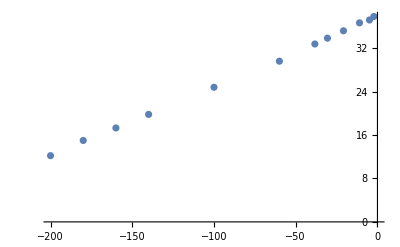

```mathematica
ListPlot[data3]
```

```mathematica
FindFormula[data,x]
```

2.07248+0.00667008 x

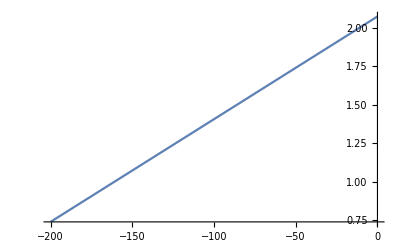

```mathematica
Plot[2.0724769+0.00667x,{x,-200,0}]
```